```mathematica
ClearAll["Global`*"]
```

## Common

```mathematica
RestylePlot[plot_Graphics,styles_List,op:OptionsPattern[Graphics]]:=Module[{x=styles},Show[MapAt[#/.{__,ln__Line}:>{Directive@Last[x=RotateLeft@x],ln}&,plot,1],op]];
```

```mathematica
dashingStyle = Dashing[{maxt/2,maxt/2-maxt/10}];
```

## Step response

### TF function

```mathematica
k=10;
T=0.01;
maxt = 0.04;
TFsimple=10/(1+0.01 s);
TF=TFsimpleTransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`$CellContext`s1FalseFalseFalseAutomaticNoneAutomatic;
TFstep=Simplify[OutputResponse[TF,UnitStep[t],t]];
TFstepf[t_]=TFstep;
TFstableValue=Limit[TFstep,t->Infinity][[1]];
```

### Horizontal Dashed Line

```mathematica
stepLineAbove=Line[{{0,TFstableValue},{maxt,TFstableValue}}];
```

### Tangent Line

```mathematica
a=0.001;
tangentLine =(D[TFstep,t]/.t->a)×(t-a) + (TFstep/.t->a);
```

### Vertical Dashed Line

```mathematica
sl=Solve[tangentLine==TFstableValue];
tangientInStable=sl[[All,1,2]][[1]];
vertLine=Line[{{tangientInStable,0},{tangientInStable,TFstableValue}}];
```

### Sizes

#### Common

```mathematica
arrowsHeads=Arrowheads[{-.035,.035}];
sizeText[text_]:=Text@TraditionalForm@Style[text, 18,Plain,FontFamily->"Times"];
```

#### Horizontal size

```mathematica
(*horSizeLeft={0,TFstableValue+0.5};
horSizeRight={tangientInStable,TFstableValue+0.5};
horSize={arrowsHeads,Arrow[{horSizeLeft,horSizeRight}]};*)
horSizeText=Text[
sizeText["T"],
{
tangientInStable,
-0.5
}
];
```

#### Vertical size

```mathematica
(*verSizeX=(tangientInStable+maxt)/2;
verSizeStart={verSizeX,0};
verSizeEnd={verSizeX,TFstableValue};
verSize={arrowsHeads,Arrow[{verSizeStart,verSizeEnd}]};*)
verSizeText=Text[
sizeText["k"],
{
-0.0005,
TFstableValue
}
];
```

### Plot

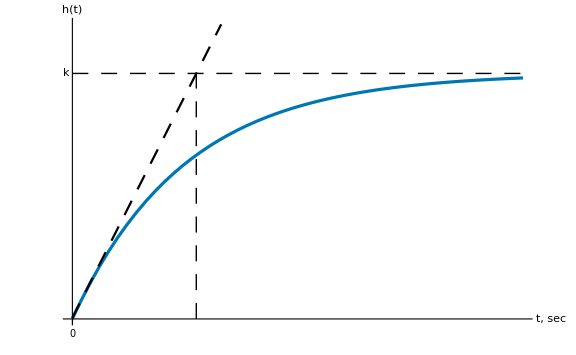

```mathematica
tickXStep=1/100;
tickYStep=1;

stepRespPic=Plot[{TFstep,tangentLine}, {t, 0, maxt},
LabelStyle->{FontFamily->"Arial",14,Black},
AxesLabel->{sizeText["t, sec"],sizeText["h(t)"]},
GridLines->None,
PlotStyle->{{RGBColor["#0077b5"],Thickness[0.004]},{Black,dashingStyle}},
PlotRange->{{0,maxt},{0,TFstableValue*1.2}},
PlotRangeClipping->False,
ImageSize->Large,
Ticks->{
Prepend[(#&@Array[{tickXStep#,}&,100]),{0,0}],
(#&@Array[{tickYStep#,}&,100])
},
Epilog->{
{Directive[Black,dashingStyle],stepLineAbove},
{Directive[Black,dashingStyle],vertLine},
{horSizeText},
{verSizeText}
}
]
```

## Bode plot

### Approx

```mathematica
tfm=TFsimple;
minF=Log10[10];
maxF=Log10[1000];
cF1=Log10[100];
xcoords={minF,cF1,maxF};
mag0=20 Log10@Abs[tfm/.s->I 0.001];
ls={mag0,0,-20 (maxF-cF1)};
ycoords=FoldList[Plus,ls[[1]],ls[[2;;-1]]];
```

### Vert Line

```mathematica
wLine=Line[{
{cF1,mag0},
{cF1,0}
}];
```

### Text

```mathematica
wText=Text[
sizeText["ω"],
{
cF1+0.05,
0.1
}
];
```

```mathematica
TText=Text[
sizeText["1/T"],
{
cF1,
mag0+1
}
];
```

### Plot

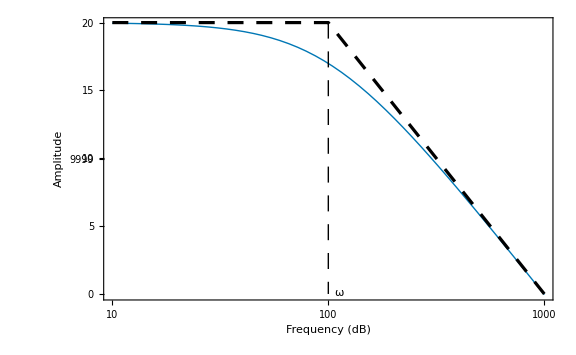

```mathematica
bodePlot=BodePlot[TF,{10,1000},PlotStyle->Thickness[0.004],ImageSize->Large];
ampBodePlot=RestylePlot[
bodePlot[[1,1,1]],
{RGBColor["#0077b5"]},
AxesLabel->{sizeText["ω"],sizeText["L(ω)"]},
LabelStyle->{
FontFamily->"Arial",14,Black
},
PlotRangeClipping->False,
ImageSize->Large,
FrameLabel->{"Frequency (dB)","Amplitude "},
ImagePadding->{{All, All},{50, 30}},
Epilog->{
{
{dashingStyle,Thickness[0.004],
Line[Thread[{xcoords,ycoords}]]
},
{
dashingStyle,
wLine
},
{wText},
{TText}
}
}
]
```